```mathematica
bdir="~/Software/BOS/build/";
```

```mathematica
GetSnapshot[n_]:=ReadList[bdir<>"snapshot_"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number,Number}]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
```

```mathematica
GetSnapshot[7]
```

{{0.500209,0.5,0.525975,0.507164,0.506907,0.525048},{1.59,0.53,0.53,1.54138,0.514865,0.571755},{2.64794,0.5,0.534924,2.64703,0.513198,0.53709},{3.71988,0.5,0.534105,3.72373,0.511673,0.535702},{0.53,1.59,0.53,0.559401,1.56174,0.521744},{1.59,1.59,0.53,1.5646,1.56887,0.56078},{2.65,1.59,0.53,2.64742,1.56665,0.508282},{3.71,1.59,0.53,3.73527,1.58575,0.510327},{0.515952,2.61951,0.5,0.511908,2.61074,0.508638},{1.59,2.65,0.53,1.54626,2.66977,0.545002},{2.65,2.65,0.53,2.67946,2.63909,0.533039},{3.71,2.65,0.53,3.69968,2.61857,0.539845},{0.569427,3.69687,0.516851,0.569427,3.69687,0.516851},{1.568,3.74911,0.505819,1.568,3.74911,0.505819},{2.65,3.71,0.53,2.65208,3.66123,0.530679},{3.71,3.71,0.53,3.76064,3.72103,0.573682}}

```mathematica
ShowSnapshot[n_]:=Row[{
ListPlot[{GetSnapshot[n][[All,{1,2}]],GetSnapshot[n][[All,{4,5}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],ListPlot[{GetSnapshot[n][[All,{1,3}]],GetSnapshot[n][[All,{4,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],
ListPlot[{GetSnapshot[n][[All,{2,3}]],GetSnapshot[n][[All,{5,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}]}]
```

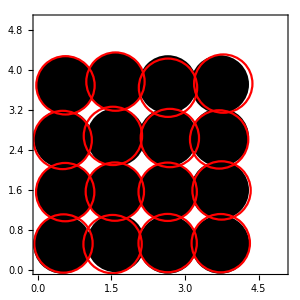
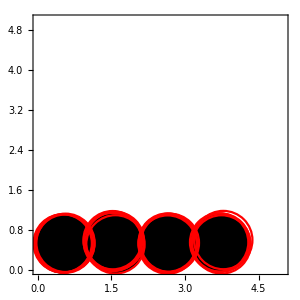
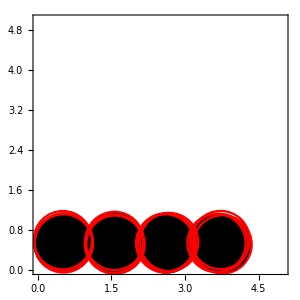

```mathematica
ShowSnapshot[10]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
Animate[ShowSnapshot[i],{i,0,nn-1,1},DisplayAllSteps->True]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
Manipulate[ShowSnapshot[i],{i,0,nn-1,1}]
```